```mathematica
(*PARTE 1:Importar r102.txt*)
data="https://people.idsia.ch/~luca/macs-vrptw/problems/r102.txt";
datos=Import[data,"Table"];
```

```mathematica
coord=datos[[10;; ,2;;3]];
Print[coord];
n=Length[coord];
Print["Número de nodos (incluye el depósito): ",n];
vehDisponibles=datos[[5,1]];
Print[vehDisponibles];
cap=datos[[5,2]];
Print[cap];
```

{{35,35},{41,49},{35,17},{55,45},{55,20},{15,30},{25,30},{20,50},{10,43},{55,60},{30,60},{20,65},{50,35},{30,25},{15,10},{30,5},{10,20},{5,30},{20,40},{15,60},{45,65},{45,20},{45,10},{55,5},{65,35},{65,20},{45,30},{35,40},{41,37},{64,42},{40,60},{31,52},{35,69},{53,52},{65,55},{63,65},{2,60},{20,20},{5,5},{60,12},{40,25},{42,7},{24,12},{23,3},{11,14},{6,38},{2,48},{8,56},{13,52},{6,68},{47,47},{49,58},{27,43},{37,31},{57,29},{63,23},{53,12},{32,12},{36,26},{21,24},{17,34},{12,24},{24,58},{27,69},{15,77},{62,77},{49,73},{67,5},{56,39},{37,47},{37,56},{57,68},{47,16},{44,17},{46,13},{49,11},{49,42},{53,43},{61,52},{57,48},{56,37},{55,54},{15,47},{14,37},{11,31},{16,22},{4,18},{28,18},{26,52},{26,35},{31,67},{15,19},{22,22},{18,24},{26,27},{25,24},{22,27},{25,21},{19,21},{20,26},{18,18}}

Número de nodos (incluye el depósito): 101

25

200

```mathematica
base=coord[[1]];
coordC=coord[[2;;]];
demanda=datos[[10;; ,4]];
ventanas=datos[[10;; ,5;;6]];
tservicio=datos[[10;; ,-1]];
```

```mathematica
Print["Dimensiones de ventanas: ",Dimensions[ventanas]];
Print["ventanas[[1]] = ",ventanas[[1]]];
Print["ventanas[[2]] = ",ventanas[[2]]];
```

Dimensiones de ventanas: {101,2}

ventanas[[1]] = {0,230}

ventanas[[2]] = {0,204}

```mathematica
Grid[datos[[1;;10]],Frame->All]
```

R102 |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  | 
VEHICLE |  |  |  |  |  |  |  |  |  | 
NUMBER | CAPACITY |  |  |  |  |  |  |  |  | 
25 | 200 |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  | 
CUSTOMER |  |  |  |  |  |  |  |  |  | 
CUST | NO. | XCOORD. | YCOORD. | DEMAND | READY | TIME | DUE | DATE | SERVICE | TIME
 |  |  |  |  |  |  |  |  |  | 
0 | 35 | 35 | 0 | 0 | 230 | 0 |  |  |  |

```mathematica
Grid[datos[[10;;]],Frame->All]
```

0 | 35 | 35 | 0 | 0 | 230 | 0
1 | 41 | 49 | 10 | 0 | 204 | 10
2 | 35 | 17 | 7 | 0 | 202 | 10
3 | 55 | 45 | 13 | 0 | 197 | 10
4 | 55 | 20 | 19 | 149 | 159 | 10
5 | 15 | 30 | 26 | 0 | 199 | 10
6 | 25 | 30 | 3 | 99 | 109 | 10
7 | 20 | 50 | 5 | 0 | 198 | 10
8 | 10 | 43 | 9 | 95 | 105 | 10
9 | 55 | 60 | 16 | 97 | 107 | 10
10 | 30 | 60 | 16 | 124 | 134 | 10
11 | 20 | 65 | 12 | 67 | 77 | 10
12 | 50 | 35 | 19 | 0 | 205 | 10
13 | 30 | 25 | 23 | 159 | 169 | 10
14 | 15 | 10 | 20 | 32 | 42 | 10
15 | 30 | 5 | 8 | 61 | 71 | 10
16 | 10 | 20 | 19 | 75 | 85 | 10
17 | 5 | 30 | 2 | 157 | 167 | 10
18 | 20 | 40 | 12 | 87 | 97 | 10
19 | 15 | 60 | 17 | 76 | 86 | 10
20 | 45 | 65 | 9 | 126 | 136 | 10
21 | 45 | 20 | 11 | 0 | 201 | 10
22 | 45 | 10 | 18 | 97 | 107 | 10
23 | 55 | 5 | 29 | 68 | 78 | 10
24 | 65 | 35 | 3 | 153 | 163 | 10
25 | 65 | 20 | 6 | 172 | 182 | 10
26 | 45 | 30 | 17 | 0 | 208 | 10
27 | 35 | 40 | 16 | 37 | 47 | 10
28 | 41 | 37 | 16 | 39 | 49 | 10
29 | 64 | 42 | 9 | 63 | 73 | 10
30 | 40 | 60 | 21 | 71 | 81 | 10
31 | 31 | 52 | 27 | 0 | 202 | 10
32 | 35 | 69 | 23 | 141 | 151 | 10
33 | 53 | 52 | 11 | 37 | 47 | 10
34 | 65 | 55 | 14 | 0 | 183 | 10
35 | 63 | 65 | 8 | 143 | 153 | 10
36 | 2 | 60 | 5 | 41 | 51 | 10
37 | 20 | 20 | 8 | 0 | 198 | 10
38 | 5 | 5 | 16 | 83 | 93 | 10
39 | 60 | 12 | 31 | 44 | 54 | 10
40 | 40 | 25 | 9 | 85 | 95 | 10
41 | 42 | 7 | 5 | 97 | 107 | 10
42 | 24 | 12 | 5 | 31 | 41 | 10
43 | 23 | 3 | 7 | 132 | 142 | 10
44 | 11 | 14 | 18 | 69 | 79 | 10
45 | 6 | 38 | 16 | 32 | 42 | 10
46 | 2 | 48 | 1 | 117 | 127 | 10
47 | 8 | 56 | 27 | 51 | 61 | 10
48 | 13 | 52 | 36 | 0 | 192 | 10
49 | 6 | 68 | 30 | 108 | 118 | 10
50 | 47 | 47 | 13 | 0 | 203 | 10
51 | 49 | 58 | 10 | 88 | 98 | 10
52 | 27 | 43 | 9 | 0 | 208 | 10
53 | 37 | 31 | 14 | 95 | 105 | 10
54 | 57 | 29 | 18 | 140 | 150 | 10
55 | 63 | 23 | 2 | 136 | 146 | 10
56 | 53 | 12 | 6 | 130 | 140 | 10
57 | 32 | 12 | 7 | 101 | 111 | 10
58 | 36 | 26 | 18 | 200 | 210 | 10
59 | 21 | 24 | 28 | 0 | 202 | 10
60 | 17 | 34 | 3 | 162 | 172 | 10
61 | 12 | 24 | 13 | 76 | 86 | 10
62 | 24 | 58 | 19 | 58 | 68 | 10
63 | 27 | 69 | 10 | 34 | 44 | 10
64 | 15 | 77 | 9 | 73 | 83 | 10
65 | 62 | 77 | 20 | 51 | 61 | 10
66 | 49 | 73 | 25 | 127 | 137 | 10
67 | 67 | 5 | 25 | 83 | 93 | 10
68 | 56 | 39 | 36 | 142 | 152 | 10
69 | 37 | 47 | 6 | 50 | 60 | 10
70 | 37 | 56 | 5 | 182 | 192 | 10
71 | 57 | 68 | 15 | 77 | 87 | 10
72 | 47 | 16 | 25 | 0 | 197 | 10
73 | 44 | 17 | 9 | 78 | 88 | 10
74 | 46 | 13 | 8 | 149 | 159 | 10
75 | 49 | 11 | 18 | 0 | 192 | 10
76 | 49 | 42 | 13 | 73 | 83 | 10
77 | 53 | 43 | 14 | 179 | 189 | 10
78 | 61 | 52 | 3 | 96 | 106 | 10
79 | 57 | 48 | 23 | 92 | 102 | 10
80 | 56 | 37 | 6 | 182 | 192 | 10
81 | 55 | 54 | 26 | 94 | 104 | 10
82 | 15 | 47 | 16 | 0 | 196 | 10
83 | 14 | 37 | 11 | 0 | 198 | 10
84 | 11 | 31 | 7 | 101 | 111 | 10
85 | 16 | 22 | 41 | 0 | 196 | 10
86 | 4 | 18 | 35 | 94 | 104 | 10
87 | 28 | 18 | 26 | 93 | 103 | 10
88 | 26 | 52 | 9 | 74 | 84 | 10
89 | 26 | 35 | 15 | 176 | 186 | 10
90 | 31 | 67 | 3 | 95 | 105 | 10
91 | 15 | 19 | 1 | 0 | 194 | 10
92 | 22 | 22 | 2 | 18 | 28 | 10
93 | 18 | 24 | 22 | 188 | 198 | 10
94 | 26 | 27 | 27 | 0 | 207 | 10
95 | 25 | 24 | 20 | 0 | 205 | 10
96 | 22 | 27 | 11 | 0 | 204 | 10
97 | 25 | 21 | 12 | 133 | 143 | 10
98 | 19 | 21 | 10 | 0 | 198 | 10
99 | 20 | 26 | 9 | 83 | 93 | 10
100 | 18 | 18 | 17 | 185 | 195 | 10

```mathematica
tiemposDeViaje=Table[N[EuclideanDistance[coord[[i]],coord[[j]]]],{i,n},{j,n}];
```

```mathematica
distanceMatrix=tiemposDeViaje;
vehicleCapacity=cap;
```

```mathematica
(***2.2 Cálculo de Tiempo/Factibilidad en una ruta***)

(*Devuelve {totalDistance,feasibleQ,arrivalTimesList}
-totalDistance=suma de distancias en la ruta
-feasibleQ indica si la ruta respeta las ventanas de tiempo
-arrivalTimesList es la lista de tiempos de llegada a cada nodo
*)
RouteCostAndFeasibility[ruta_,distanceMat_,twList_,speed_,serviceTime_:0]:=Module[{distTotal=0.,arrivalTime=0.,feasible=True,arrivalTimes={}},Do[Module[{origen=ruta[[i]],destino=ruta[[i+1]]},(*Parche:si'destino' no está en 1..Length[twList],la ruta se vuelve no factible y paramos.*)If[destino<1||destino>Length[twList],feasible=False;
Return[{distTotal,feasible,arrivalTimes},Module];];
distTotal+=distanceMat[[origen,destino]];
arrivalTime+=distanceMat[[origen,destino]]/speed;
If[arrivalTime<twList[[destino,1]],arrivalTime=twList[[destino,1]]];
If[arrivalTime>twList[[destino,2]],feasible=False];
arrivalTime+=serviceTime;
AppendTo[arrivalTimes,arrivalTime];],{i,1,Length[ruta]-1}];
{distTotal,feasible,arrivalTimes}];

(***2.3 Costo de toda la solución (múltiples rutas)***)
SolutionCostVRPTW[solution_,distanceMat_,twList_,speed_]:=Module[{totalDist=0.,feasible=True,rc},Do[rc=RouteCostAndFeasibility[ruta,distanceMat,twList,speed];
totalDist+=rc[[1]];
If[rc[[2]]===False,feasible=False;],{ruta,solution}];
If[feasible,totalDist,Infinity]]

(*2.4 Inserción Greedy con Capacidad y Ventanas*)(*Dado un'solution' (lista de rutas),intenta insertar'cliente' en la mejor (ruta,posición) que no viole Capacidad ni Ventanas.Retorna {newSolution,insertedQ}.*)
InsertClientBestPosition[solution_,cliente_,distanceMat_,demands_,twList_,vehCap_,depotNode_,speed_]:=Module[{bestSol=solution,bestCost=Infinity,inserted=False,ruta,newRuta,i,tempSol,costTemp},(*Iterar sobre cada ruta en la solución*)Do[ruta=solution[[r]];
(*Chequeo de capacidad actual de la ruta*)If[CapacityUsed[DeleteCases[ruta,depotNode],demands]+demands[[cliente]]<=vehCap,(*Probamos insertar el cliente en todas las posiciones posibles de la ruta,excepto no partir ni terminar sin el depot*)For[i=1,i<Length[ruta],i++,newRuta=Insert[ruta,cliente,i+1];
(*Crear una solución temporal con la nueva ruta*)tempSol=ReplacePart[solution,r->newRuta];
(*Calcular el costo de la solución temporal*)costTemp=SolutionCostVRPTW[tempSol,distanceMat,twList,speed];
(*Si el costo es mejor que el mejor costo encontrado hasta ahora,actualizar la mejor solución y costo*)If[costTemp<bestCost,bestCost=costTemp;
bestSol=tempSol;
inserted=True;
Print["Cliente ",cliente," insertado en ruta ",r," posición ",i+1," con nuevo costo ",bestCost];];];],{r,1,Length[solution]}];
(*Retornar la mejor solución encontrada y si se insertó el cliente*){bestSol,inserted}]

(*2.5 Heurística de Construcción (Greedy+Múltiples Rutas)*)
ConstructSolutionVRPTW[distanceMat_,demands_,twList_,depot_,vehCap_,speed_]:=Module[{sol={},notAssigned,cl,attemptSol,insertedQ,newRoute,rc},notAssigned=DeleteCases[Range[Length[demands]],depot];
sol={};
While[notAssigned=!={},(*Si no hay rutas abiertas,abrimos una con {depot,depot}*)If[sol=={},AppendTo[sol,{depot,depot}]];
(*Tomamos un cliente de notAssigned al azar*)cl=RandomChoice[notAssigned];
(*Print["Intentando asignar el cliente ",cl];*)
(*Intentar insertar el cliente en las rutas existentes*){attemptSol,insertedQ}=InsertClientBestPosition[sol,cl,distanceMat,demands,twList,vehCap,depot,speed];
If[insertedQ,(*Se insertó en una ruta existente*)sol=attemptSol;
notAssigned=DeleteCases[notAssigned,cl];
Print["Cliente ",cl," insertado en una ruta existente."];,(*No cupo en ninguna=>intentar abrir una nueva ruta*)newRoute={depot,cl,depot};
rc=RouteCostAndFeasibility[newRoute,distanceMat,twList,speed];
If[rc[[2]]==True,AppendTo[sol,newRoute];
notAssigned=DeleteCases[notAssigned,cl];
(***Print["Cliente ",cl," asignado a una nueva ruta. Costo: ",rc[[1]]];,***)
(*Si no es factible,no se puede asignar*)
(***Print["Cliente ",cl," no puede ser asignado a una nueva ruta. Omite."];***)
notAssigned=DeleteCases[notAssigned,cl]; (*O mantenerlo en notAssigned*)];
];];
sol]
			

(***2.6 Búsqueda Local:ejemplos sencillos***)
(*Movimientos sencillos:-2-opt intra-ruta-Mover un cliente de la ruta i a la ruta j Se pueden añadir muchas mejoras.*)
TwoOptIntraRoute[ruta_,distanceMat_,twList_,speed_]:=Module[{bestRoute=ruta,bestCost,newRoute,i,j},bestCost=RouteCostAndFeasibility[ruta,distanceMat,twList,speed][[1]];
For[i=2,i<Length[ruta]-2,i++,For[j=i+1,j<Length[ruta]-1,j++,newRoute=Join[ruta[[1;;i-1]],Reverse[ruta[[i;;j]]],ruta[[j+1;;]]];
Module[{c=RouteCostAndFeasibility[newRoute,distanceMat,twList,speed]},If[c[[2]]&&c[[1]]<bestCost,bestCost=c[[1]];
bestRoute=newRoute;];];];];
bestRoute]

MoveOneClientBetweenRoutes[sol_,distanceMat_,twList_,demands_,vehCap_,depotNode_,speed_]:=Module[{bestSol=sol,bestCost,costSol,i,j,r1,r2,route1,route2,newRoute1,newRoute2,client,k,pos},bestCost=SolutionCostVRPTW[sol,distanceMat,twList,speed];
(*Recorremos pares de rutas*)For[r1=1,r1<=Length[sol],r1++,For[r2=1,r2<=Length[sol],r2++,If[r1!=r2,route1=sol[[r1]];
route2=sol[[r2]];
(*Recorremos clientes en route1 (excepto el depot)*)For[k=2,k<=Length[route1]-1,k++,client=route1[[k]];
(*Chequear si capacity route2 lo tolera*)If[CapacityUsed[DeleteCases[route2,depotNode],demands]+demands[[client]]<=vehCap,(*Probamos quitar client de route1 e insertarlo en route2 en distintas posiciones*)For[pos=2,pos<Length[route2],pos++,newRoute1=Delete[route1,k];
newRoute2=Insert[route2,client,pos];
Module[{tempSol=ReplacePart[sol,{r1->newRoute1,r2->newRoute2}],costTemp},costTemp=SolutionCostVRPTW[tempSol,distanceMat,twList,speed];
If[costTemp<bestCost,bestCost=costTemp;
bestSol=tempSol;];];];];];];];];
bestSol]

(***2.7 Búsqueda Local Compuesta***)
LocalSearchVRPTW[sol_,distanceMat_,twList_,demands_,vehCap_,depotNode_,speed_]:=Module[{improvedSol=sol,newSol,changed=True},While[changed,changed=False;
(*1) Intra-ruta 2-opt en cada ruta*)Do[Module[{r0=improvedSol[[r]],rOpt},rOpt=TwoOptIntraRoute[r0,distanceMat,twList,speed];
If[rOpt=!=r0,improvedSol=ReplacePart[improvedSol,r->rOpt];
changed=True;];],{r,1,Length[improvedSol]}];
(*2) Mover clientes entre rutas*)newSol=MoveOneClientBetweenRoutes[improvedSol,distanceMat,twList,demands,vehCap,depotNode,speed];
If[newSol=!=improvedSol,improvedSol=newSol;
changed=True;];];
improvedSol]

(*3) Definir el Factor de Velocidad*)
speed=1; (*Ajustar este valor según se necesite*)

(*4) Fase GRASP*)
GRASPVRPTW[distanceMat_,demands_,twList_,depot_,vehCap_,speed_,maxIter_]:=Module[{bestSol,(*guardará la mejor solución final*)bestCost=Infinity,iter,solConstr,solLocal,costLocal,bestCosts={},(*lista para ir acumulando el “mejor costo” por iteración*)bestNumVeh={},(*lista para guardar el número de vehículos de la mejor solución en cada iter*)iterationTimes={},(*lista para guardar el tiempo de CPU por iter*)startTime,iterTime},For[iter=1,iter<=maxIter,iter++,(*Medimos tiempo al inicio de cada iteración*)startTime=AbsoluteTime[];
(*1) Construcción Rápida/Greedy (o RCL si deseas)*)solConstr=ConstructSolutionVRPTW[distanceMat,demands,twList,depot,vehCap,speed];
(*2) Búsqueda Local (puedes también meter routeElimination si lo implementas)*)solLocal=LocalSearchVRPTW[solConstr,distanceMat,twList,demands,vehCap,depot,speed];
(*3) Cálculo del costo de la solución local*)costLocal=SolutionCostVRPTW[solLocal,distanceMat,twList,speed];
(*4) Comparamos con la mejor solución hasta ahora*)If[costLocal<bestCost,bestCost=costLocal;
bestSol=solLocal;];
(*Guardar el “mejor costo” actual en la iteración*)AppendTo[bestCosts,bestCost];
(*Podemos contar cuántos vehículos tiene la mejorSol:Por ejemplo,length[bestSol].O si cada subruta es {dep,...,dep},su “longitud” de sub-listas es # de vehículos.*)AppendTo[bestNumVeh,Length[bestSol]];
(*Mides el tiempo invertido en esta iteración*)iterTime=AbsoluteTime[]-startTime;
AppendTo[iterationTimes,iterTime];
(*Mostrar el progreso en cada iteración*)Print["Iteración: ",iter," - Mejor costo actual: ",bestCost," - Vehículos: ",Length[bestSol]," - Tiempo iter (s): ",iterTime//N];];(*fin del For*)(*OPCIONAL:Imprimir un resumen final*)Print["GRASP finalizado. Mejor costo encontrado: ",bestCost];
Print["Número de vehículos de la mejor solución: ",Length[bestSol]];
(*Devolvemos en un “Package” el bestSol,bestCost y las listas de estadística para luego graficar o analizar.*){bestSol,bestCost,bestCosts,bestNumVeh,iterationTimes}]
```

```mathematica
depotNode=1;
demands=demanda;
serviceTimes=tservicio;
```

```mathematica
timeWindows=datos[[10;; ,{5,6}]];
Print[Dimensions[timeWindows]];
```

{101,2}

```mathematica
Dimensions[ventanas]
```

{101,2}

```mathematica
maxIter=25;
{solBest,costBest,costPerIter,vehPerIter,timePerIter}=GRASPVRPTW[distanceMatrix,demands,timeWindows,depotNode,vehicleCapacity,speed,maxIter];
```

Iteración: 1 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.319146

Iteración: 2 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.34807

Iteración: 3 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.362032

Iteración: 4 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.333108

Iteración: 5 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.345078

Iteración: 6 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.327125

Iteración: 7 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.353055

Iteración: 8 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.424865

Iteración: 9 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.386967

Iteración: 10 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.451789

Iteración: 11 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.446804

Iteración: 12 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.488699

Iteración: 13 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.410895

Iteración: 14 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.353056

Iteración: 15 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.359039

Iteración: 16 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.439825

Iteración: 17 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.329121

Iteración: 18 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.356047

Iteración: 19 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.437828

Iteración: 20 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.32912

Iteración: 21 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.339093

Iteración: 22 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.308176

Iteración: 23 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.359039

Iteración: 24 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.389955

Iteración: 25 - Mejor costo actual: 4989.42 - Vehículos: 101 - Tiempo iter (s): 0.521605

GRASP finalizado. Mejor costo encontrado: 4989.42

Número de vehículos de la mejor solución: 101

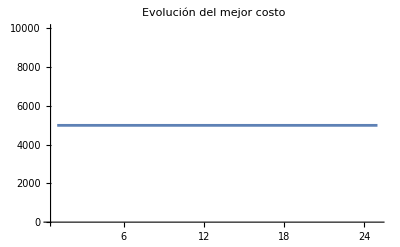

```mathematica
(*Graficar la evolución del costo*)ListLinePlot[costPerIter,PlotRange->All,PlotLabel->"Evolución del mejor costo"]
```

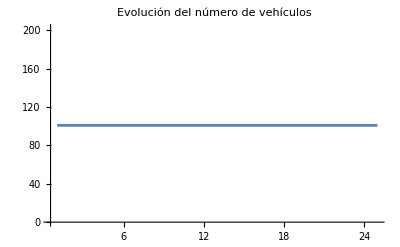

```mathematica
(*Graficar la evolución del # de vehículos*)ListLinePlot[vehPerIter,PlotRange->All,PlotLabel->"Evolución del número de vehículos"]
```

```mathematica
(*Ver tiempos por iteración*)
timePerIter
```

{0.319146,0.34807,0.3620316,0.333108,0.345078,0.327125,0.353055,0.4248647,0.3869666,0.4517892,0.4468035,0.4886987,0.4108953,0.353056,0.3590387,0.4398246,0.329121,0.3560467,0.4378279,0.32912,0.339093,0.308176,0.359039,0.3899551,0.5216046}

```mathematica
(*Verificar factibilidad de una ruta simple*)
testRoute={depotNode,2,depotNode};
rc=RouteCostAndFeasibility[testRoute,distanceMatrix,timeWindows,speed];
Print["Factibilidad de la ruta ",testRoute,": ",rc[[2]],", Costo: ",rc[[1]]];
```

Factibilidad de la ruta {1,2,1}: True, Costo: 30.4631

```mathematica
testRoute={1,2,1};
rc=RouteCostAndFeasibility[testRoute,distanceMatrix,timeWindows,speed];
Print["Factibilidad: ",rc[[2]],", Costo: ",rc[[1]]];
```

Factibilidad: True, Costo: 30.4631

```mathematica
(*Verificar factibilidad de cada ruta en la mejor solución*)factibilidadFinal=RouteCostAndFeasibility[#,distanceMatrix,twList,speed]&/@bestSolution;
Print["Factibilidad de cada ruta final: ",factibilidadFinal];
```

Factibilidad de cada ruta final: bestSolution

```mathematica
factibilidadFinal=RouteCostAndFeasibility[#,distanceMatrix,twList,speed]&/@bestSolution;
Print["Factibilidad de cada ruta final: ",factibilidadFinal];
```

Factibilidad de cada ruta final: bestSolution